# Machine Learning from the Ground Up

```mathematica
Directory[];
(* You may need to change this to the correct directory. *)
SetDirectory[".\\prog\\mathematica\\mathematica-models\\math299m\\Final Project - ML from the Ground Up"];
```

```mathematica
RealTime=True;
```

What is machine learning actually trying to do?

Let’s say you want to buy a house. What factors make a house more expensive?

Neighborhood?

Number of Rooms?

Square footage of the yard?

Area of the pool?

If you’re mathematically inclined, you might try to come up with some model that matches the predictions. However, in machine learning, it’s all about learning from the right answers, so it’s all about the data!

```mathematica
HousingData=Import["housing.csv"];
HousingFeatures=HousingData[[1;;1,2;;-2]];
HousingX=HousingData[[2;;-1,2;;-2]];
HousingLabel=HousingData[[1;;1,-1;;-1]];
HousingY=HousingData[[2;;-1,-1;;-1]];
Print["Original Data:  "<>ToString[Dimensions[HousingData]]]
Print["Housing Input:  "<>ToString[Dimensions[HousingX]]]
Print["Housing Output: "<>ToString[Dimensions[HousingY]]]
```

Original Data:  {1461, 15}

Housing Input:  {1460, 13}

Housing Output: {1460, 1}

This data lists a bunch of potentially useful features:

```mathematica
Transpose[HousingFeatures]//MatrixForm//Magnify
```

(Lot Area
Overall Quality
Overall Condition
Year Built
Basement Area
Ground Floor Area
Second Floor Area
Living Area
Bathrooms
Bedrooms
Fireplaces
Garage Area
Deck Area)

And also important, the labels we have (the right answers):

```mathematica
HousingLabel//MatrixForm//Magnify
```

(Sale Price)

So let's see if we can predict sale price from these features then.

First Step: Exploratory Data Analysis

This is about what the data looks like. We already saw what the “features” are, there are lots of ways we can visualize it.

What does the data literally look like?

```mathematica
HousingData[[1;;40]]//TableForm
```

House Id | Lot Area | Overall Quality | Overall Condition | Year Built | Basement Area | Ground Floor Area | Second Floor Area | Living Area | Bathrooms | Bedrooms | Fireplaces | Garage Area | Deck Area | Sale Price
1 | 8450 | 7 | 5 | 2003 | 856 | 856 | 854 | 1710 | 4 | 3 | 0 | 548 | 0 | 208500
2 | 9600 | 6 | 8 | 1976 | 1262 | 1262 | 0 | 1262 | 3 | 3 | 1 | 460 | 298 | 181500
3 | 11250 | 7 | 5 | 2001 | 920 | 920 | 866 | 1786 | 4 | 3 | 1 | 608 | 0 | 223500
4 | 9550 | 7 | 5 | 1915 | 756 | 961 | 756 | 1717 | 2 | 3 | 1 | 642 | 0 | 140000
5 | 14260 | 8 | 5 | 2000 | 1145 | 1145 | 1053 | 2198 | 4 | 4 | 1 | 836 | 192 | 250000
6 | 14115 | 5 | 5 | 1993 | 796 | 796 | 566 | 1362 | 3 | 1 | 0 | 480 | 40 | 143000
7 | 10084 | 8 | 5 | 2004 | 1686 | 1694 | 0 | 1694 | 3 | 3 | 1 | 636 | 255 | 307000
8 | 10382 | 7 | 6 | 1973 | 1107 | 1107 | 983 | 2090 | 4 | 3 | 2 | 484 | 235 | 200000
9 | 6120 | 7 | 5 | 1931 | 952 | 1022 | 752 | 1774 | 2 | 2 | 2 | 468 | 90 | 129900
10 | 7420 | 5 | 6 | 1939 | 991 | 1077 | 0 | 1077 | 2 | 2 | 2 | 205 | 0 | 118000
11 | 11200 | 5 | 5 | 1965 | 1040 | 1040 | 0 | 1040 | 2 | 3 | 0 | 384 | 0 | 129500
12 | 11924 | 9 | 5 | 2005 | 1175 | 1182 | 1142 | 2324 | 4 | 4 | 2 | 736 | 147 | 345000
13 | 12968 | 5 | 6 | 1962 | 912 | 912 | 0 | 912 | 2 | 2 | 0 | 352 | 140 | 144000
14 | 10652 | 7 | 5 | 2006 | 1494 | 1494 | 0 | 1494 | 2 | 3 | 1 | 840 | 160 | 279500
15 | 10920 | 6 | 5 | 1960 | 1253 | 1253 | 0 | 1253 | 3 | 2 | 1 | 352 | 0 | 157000
16 | 6120 | 7 | 8 | 1929 | 832 | 854 | 0 | 854 | 1 | 2 | 0 | 576 | 48 | 132000
17 | 11241 | 6 | 7 | 1970 | 1004 | 1004 | 0 | 1004 | 2 | 2 | 1 | 480 | 0 | 149000
18 | 10791 | 4 | 5 | 1967 | 0 | 1296 | 0 | 1296 | 2 | 2 | 0 | 516 | 0 | 90000
19 | 13695 | 5 | 5 | 2004 | 1114 | 1114 | 0 | 1114 | 3 | 3 | 0 | 576 | 0 | 159000
20 | 7560 | 5 | 6 | 1958 | 1029 | 1339 | 0 | 1339 | 1 | 3 | 0 | 294 | 0 | 139000
21 | 14215 | 8 | 5 | 2005 | 1158 | 1158 | 1218 | 2376 | 4 | 4 | 1 | 853 | 240 | 325300
22 | 7449 | 7 | 7 | 1930 | 637 | 1108 | 0 | 1108 | 1 | 3 | 1 | 280 | 0 | 139400
23 | 9742 | 8 | 5 | 2002 | 1777 | 1795 | 0 | 1795 | 2 | 3 | 1 | 534 | 171 | 230000
24 | 4224 | 5 | 7 | 1976 | 1040 | 1060 | 0 | 1060 | 2 | 3 | 1 | 572 | 100 | 129900
25 | 8246 | 5 | 8 | 1968 | 1060 | 1060 | 0 | 1060 | 2 | 3 | 1 | 270 | 406 | 154000
26 | 14230 | 8 | 5 | 2007 | 1566 | 1600 | 0 | 1600 | 2 | 3 | 1 | 890 | 0 | 256300
27 | 7200 | 5 | 7 | 1951 | 900 | 900 | 0 | 900 | 2 | 3 | 0 | 576 | 222 | 134800
28 | 11478 | 8 | 5 | 2007 | 1704 | 1704 | 0 | 1704 | 3 | 3 | 1 | 772 | 0 | 306000
29 | 16321 | 5 | 6 | 1957 | 1484 | 1600 | 0 | 1600 | 2 | 2 | 2 | 319 | 288 | 207500
30 | 6324 | 4 | 6 | 1927 | 520 | 520 | 0 | 520 | 1 | 1 | 0 | 240 | 49 | 68500
31 | 8500 | 4 | 4 | 1920 | 649 | 649 | 668 | 1317 | 1 | 3 | 0 | 250 | 0 | 40000
32 | 8544 | 5 | 6 | 1966 | 1228 | 1228 | 0 | 1228 | 2 | 3 | 0 | 271 | 0 | 149350
33 | 11049 | 8 | 5 | 2007 | 1234 | 1234 | 0 | 1234 | 2 | 3 | 0 | 484 | 0 | 179900
34 | 10552 | 5 | 5 | 1959 | 1398 | 1700 | 0 | 1700 | 3 | 4 | 1 | 447 | 0 | 165500
35 | 7313 | 9 | 5 | 2005 | 1561 | 1561 | 0 | 1561 | 3 | 2 | 1 | 556 | 203 | 277500
36 | 13418 | 8 | 5 | 2004 | 1117 | 1132 | 1320 | 2452 | 4 | 4 | 1 | 691 | 113 | 309000
37 | 10859 | 5 | 5 | 1994 | 1097 | 1097 | 0 | 1097 | 2 | 3 | 0 | 672 | 392 | 145000
38 | 8532 | 5 | 6 | 1954 | 1297 | 1297 | 0 | 1297 | 2 | 3 | 1 | 498 | 0 | 153000
39 | 7922 | 5 | 7 | 1953 | 1057 | 1057 | 0 | 1057 | 2 | 3 | 0 | 246 | 0 | 109000

Useful. Real useful.

But we can do better. There’s a very common method that’s used to visualize tabular data in space. We can treat each example (each house) as a vector:

```mathematica
HousingX[[1]]//MatrixForm//Magnify
Print["Vector Dimension: "<>ToString[Length[HousingX[[1]]]]]
```

(8450
7
5
2003
856
856
854
1710
4
3
0
548
0)

Vector Dimension: 13

But this is a 13-dimensional vector space we’re trying to look at!! Are you able to visualize 13 dimensions?!? No, probably not, so we want to reduce the number of dimensions to 2 or 3 so that we can actually imagine it. We use something called tSNE (t-Distributed Stochastic Neighbor Embedding) to reduce the dimensions to 3. Now, we can visualize the data, but each dimension means less (it’s some transformation of the original dimensions).

```mathematica
Check[
tsne3D=Import["tsne.mx"],
Module[{},
tsne3D=DimensionReduce[HousingX,3,Method->"TSNE"];
Export["tsne.mx",tsne3D]
]];
```

```mathematica
ListPointPlot3D[tsne3D,ImageSize->Full,Axes->False,Boxed->False,ColorFunction->Function[{x,y,z},Hue[Nearest[tsne3D->HousingY,{x,y,z}]]]]
```

-Graphics3D-

Okay...cool, I guess? There are more useful insights we can get from the data though (tSNE usually’s useful, but it’s easier to use for classification problems). Let’s do some statistics:

```mathematica
FindBarProp[p_,d_]:=Table[Labeled[p[d[[;;,x]]],HousingFeatures[[1]][[x]]],{x,1,Dimensions[HousingFeatures][[2]]}];
FindBarProp[p_]:=FindBarProp[p,HousingX]
```

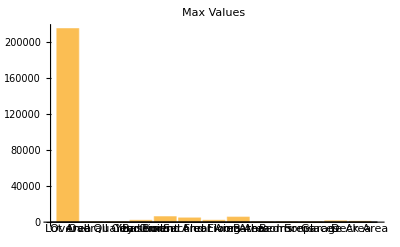

```mathematica
BarChart[FindBarProp[Max],ImageSize->Full,PlotLabel->"Max Values"]
```

Yikes! Our max values are very different (and so are our standard deviations). This will make it hard for us to determine what’s important and what’s not. For example, if we train a linear model on this data, we might think that because Lot Area has a large weight, it’s important. We can’t tell if it’s important or not, because the values for Lot Area are just so huge! So instead, let’s standardize our data to be 0-mean, unit variance.

```mathematica
FeatureMeans=Table[Mean[HousingX[[;;,x]]]//N,{x,1,Dimensions[HousingFeatures][[2]]}];
FeatureStandardDeviations=Table[StandardDeviation[HousingX[[;;,x]]]//N,{x,1,Dimensions[HousingFeatures][[2]]}];
trHousingX=Map[(#-FeatureMeans)/FeatureStandardDeviations&,HousingX];
```

After we do this, does our picture of the data change?

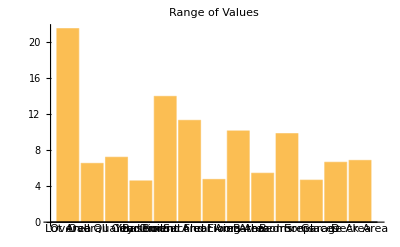

```mathematica
BarChart[FindBarProp[Max[#]-Min[#]&,trHousingX],ImageSize->Full,PlotLabel->"Range of Values"]
```

Ah, much better. And our literal picture?

```mathematica
Check[tsne3Dtr=Import["tsneTransformed.mx"],
Module[{},
tsne3Dtr=DimensionReduce[trHousingX,3,Method->"TSNE"];
Export["tsneTransformed.mx",tsne3Dtr]
]];
```

```mathematica
ListPointPlot3D[tsne3Dtr,PlotRange->Full,ImageSize->Full,Axes->False,Boxed->False,ColorFunction->Function[{x,y,z},Hue[Nearest[tsne3Dtr->HousingY,{x,y,z}]]]]
```

-Graphics3D-

You can start to see some real structure: there seems to be 2 bands, and overall it’s in a twisted helix or partial toroid of some kind.

We can quickly train and run a model with Mathematica that tries to fit this data, but we don’t have time to write that right now.

## Function Approximation

That was just an introduction to looking at data, but we’re going to step back and look at a vastly smaller dataset: a bunch of points in ℝ^2.

```mathematica
Xtr={{0,-1},{10,5},{2,3},{20,40},{14,30},{5,2},{7,7},{13,34},{12.5,22},{12,23},{11,24},{14.5,20},{16, 27},{12.25,12},{1,2},{17,20},{18,34},{19,34},{25,50},{23,45},{24,55}};
LinearMSE[h_,d_]:=Length[d]^-1 Fold[#1+EuclideanDistance[h[#2[[1]]],#2[[2]]]&,0,d];
LinearMSE[h_]:=LinearMSE[h,Xtr];
DataLandscape=ListPlot[Xtr];
LossLandscape=ContourPlot[LinearMSE[W #+b&],{W,-5,5},{b,-25,25},Contours->20];
```

Linear Approximation in ℝ^2

Let’s set up what our first simple model looks like. We want to use a linear model to predict a single continuous output (regression). For now, we’ll just try to match a set of data points in ℝ^2 using a linear model (this isn’t really that advanced machine learning, it’s just statistical regression).

What we’re trying to do is just tune W and b so that Wx+b closely approximates our training data. Try doing that manually below (the bar graph shows the cost function--try to minimize this).

```mathematica
Manipulate[
GraphicsGrid[{{
Show[
Plot[W x+b,{x,0,26},
PlotRange->{0,60},
AspectRatio->1
],
DataLandscape
],
BarChart[{Labeled[LinearMSE[W #+b&],LinearMSE[W #+b&],Above]},
PlotRange->{0,If[micro,10,120]},
ColorFunction->"TemperatureMap"]
}},ImageSize->Full],
{{W,0,"Weight Matrix (W)"},-Abs[b]/5,5},
{{b,25,"Bias Vector (b)"},-25,25},
{{micro,False,"Micro-Adjustment"},{True,False}}
]//Magnify
```

Even though we can pretty easily visualize our “guess” (called our hypothesis function), there’s still something else we really would like to see. Right now, we’re just guessing at the changes to W and b that will improve our model. We’d really like to see what the cost function looks like! Instead of making random guesses, we move towards the pit of the loss landscape.

```mathematica
Manipulate[
GraphicsGrid[{{
Show[
Plot[W x+b,{x,0,26},
PlotRange->{0,60},
AspectRatio->1
],
DataLandscape
],
BarChart[{Labeled[LinearMSE[W #+b&],LinearMSE[W #+b&],Above]},
PlotRange->{0,If[micro,10,120]},
ColorFunction->"TemperatureMap"],
Show[
LossLandscape,
Graphics[{PointSize[Large],Point[{W,b}]}]
]
}},ImageSize->Full],
{{W,0,"Weight Matrix (W)"},-Abs[b]/5,5},
{{b,25,"Bias Vector (b)"},-25,25},
{{micro,False,"Micro-Adjustment"},{True,False}}
]//Magnify
```

Basic Feature Engineering

So far, this is really just statistics. Here’s some data, what kind of function matches it? One thing that’s commonly done in machine learning is feature engineering. Just using x isn’t enough, so why not also include other “versions” of x?

Like,
	x^2,x^3,x^4,...,x^n,√x,etc.
	
Let’s just add a few polynomials to our previous model and see if we can’t get the loss to go down. Now that we have 4 parameters though (W1,W2,W3,b), we’ll visualize them 2 at a time (unless you have a 4-dimensional brain?).

```mathematica
Manipulate[
GraphicsGrid[{{
Show[
DataLandscape,
Plot[W1 x+W2 x^2+W3 x^3+b,{x,0,26},
PlotRange->{0,60},
AspectRatio->1
]
],
BarChart[{Labeled[LinearMSE[W1 #+W2 #^2+W3 #^3+b&],LinearMSE[W1 #+W2 #^2+W3 #^3+b&],Above]},
PlotRange->{0,If[micro,10,200]},
ColorFunction->"TemperatureMap"],
Show[
ContourPlot[LinearMSE[W1 #+W2 #^2+W3 #^3+b&],{W1,-5,5},{W2,-1,1},Contours->10],
Graphics[{PointSize[Large],Point[{W1,W2}]}]
],
Show[
ContourPlot[LinearMSE[W1 #+W2 #^2+W3 #^3+b&],{W3,-1/5,1/5},{b,-25,25},Contours->10],
Graphics[{PointSize[Large],Point[{W3,b}]}]
]
}},ImageSize->Full],
{{W1,0,"Weight Matrix 1 (W1)"},-5,5,.1},
{{W2,0,"Weight Matrix 2 (W2)"},-1,1,.01},
{{W3,0,"Weight Matrix 3 (W3)"},-1/5,1/5,.001},
{{b,25,"Bias Vector (b)"},-25,25,1},
{{micro,False,"Micro-Adjustment"},{True,False}}
]//Magnify
```

We can get a slightly better theoretical minimum if we add more features. The issue is, we can ALWAYS get a better fit on our dataset by adding more features.

So there's a huge danger here ... look at what happens when we allow as many polynomial terms as we have training examples (we end up with a perfect interpolation) :

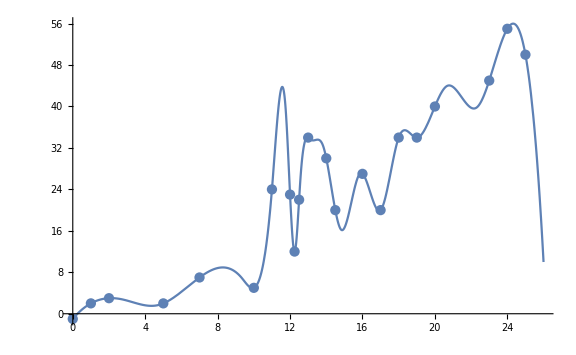

```mathematica
Module[{h},
h=Interpolation[Xtr,Method->"Spline"];
Show[
Plot[h[x],{x,0,26}],
ListPlot[Xtr],
ImageSize->Large
]//Magnify
]
```

And what's our error?

```mathematica
Module[{h},
h=Interpolation[Xtr,Method->"Spline"];
LinearMSE[h]
]//Magnify
```

1.21596×10^-15

Meaning? If we have enough features, we can pretty much approximate any function/dataset perfectly. THAT’S BAD! I think we can all agree that the above curve does not really match what we intuitively think the data is describing; it’s probably also modeling all the noise in our data. For example,

```mathematica
Module[{h},
h=Interpolation[Xtr,Method->"Spline"];

h[11.5]-h[10]
]//Magnify
```

38.2834

Even though 10 and 11.5 are pretty close to each other, the predicted value differs by almost 40 units!

(I’ve cheated a little here and just used the spline interpolation of the data points. It’s not quite the same as what I’m saying, but it generalizes anyway.)

There’s a fundamental tradeoff going on here that also applies to other types of machine learning: TPR vs. FPR.
	true positive rate (TPR) = (true positives)/(true positives + false negatives) (how many of the good ones did I get?)
	false positive rate (FPR) = (false positives)/(false positives + true negatives) (how many of the bad ones did I get?)

We want to maximize the TPR (get as many of the correct ones as possible; miss out on as few good ones as possible) and minimize  the FPR (get as few of the wrong ones incorrect; exclude as many bad ones as possible). If this seems confusing, don’t worry, it is! (And it comes from the confusion matrix, so aptly named.)

There are other projects in Mathematica that describe interpolation and getting best-fits on our data, but machine learning is not actually about that.

A good one on Fourier series:

```mathematica
["http://bilimneguzellan.net/purrier-series-meow-and-making-images-speak/"](http://bilimneguzellan.net/purrier-series-meow-and-making-images-speak/)
```

Evaluation

It’s important to know: the goal of machine learning is not to get the best performance on our training data. The point is to generalize well to outside samples.

```mathematica
Xte=Map[{#,2.263#-4.65}&,{5,7,9,15,22,28}];
```

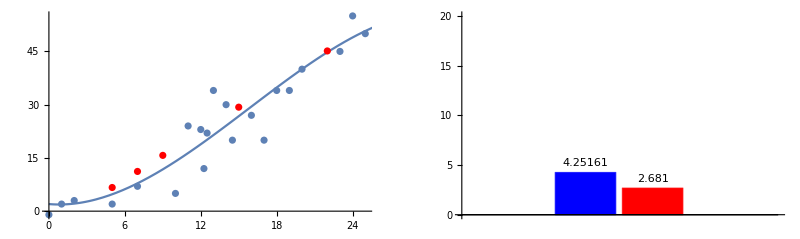

```mathematica
GraphicsGrid[{{Show[
DataLandscape,
Plot[-0.3 x+0.19 x^2-0.004 x^3+2,{x,0,26},
PlotRange->{0,60},
AspectRatio->1
],
ListPlot[Xte,PlotStyle->Red]
],
Show[
BarChart[{Labeled[LinearMSE[-0.3 #+0.19 #^2-0.004 #^3+2&],LinearMSE[-0.3 #+0.19 #^2-0.004 #^3+2&],Above],Labeled[LinearMSE[-0.3 #+0.19 #^2-0.004 #^3+2&,Xte],LinearMSE[-0.3 #+0.19 #^2-0.004 #^3+2&,Xte],Above]},
PlotRange->{0,20},
ChartStyle->{Blue,Red}]
]
}},ImageSize->Full]
```

So the reason we believe this is a good model for the function is because our test set (the dots in red) has a lower mean loss, NOT because of a low training loss.

There are a couple of other ways we evaluate, but I leave those to your curiosity. There’s an important hidden issue here though, that is (purposefully, by the notebook creator) obfuscated. What happens if our test input (or actual input) has a different distribution than our training data? Above, the red test dots were are drawn from roughly the same distribution, but that’s usually not the case in reality. (I mean things like if we only ever see cats in trees, but then see a cat on carpet, that’s a very different distribution of input.)

Let me unhide the issue...

```mathematica
Manipulate[
Show[
Plot[-0.3 x+0.19 x^2-0.004 x^3+2,{x,-b,25+b},
PlotRange->{0,60},
AspectRatio->.5
],
DataLandscape,
ListPlot[Xte,PlotStyle->Red],ImageSize->Full
],
{{b,0,"Reveal"},0,20}
]
```

Whoa, what happened to our model? It turns out, even though our model’s really good in the original distribution, if we go outside that range even a little, we see behavior that we’re probably not expecting. This is part of the problem of generalization, where we want to make sure our model works for as diverse inputs as possible, even though we don’t see the full range of them.

Optimization

One last thing before we get to cooler stuff. So far, you' ve just been literally manually tuning models. Instead of doing that, let' s figure out how ML algorithms tackle the problem.

Let’s say we have some loss function:

```mathematica
J[x_,y_]:=0.001(-5+10x-51 x^2-.8 x^3+0.01 x^4)+0.1 y^2+0.0001 x^2 y+400;
DynamicModule[{p={100,100},LossSurface,LossFunction},
LossSurface=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossFunction=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Dynamic[
GraphicsGrid[{{
Show[
LossSurface,
Graphics3D[{PointSize[.05],Dynamic[Point[Flatten[{p,J[p[[1]],p[[2]]]}]]]}]
],
Show[
LossFunction,
Graphics[Locator[Dynamic[p]]]
],
BarChart[{Labeled[J[p[[1]],p[[2]]],J[p[[1]],p[[2]]],Above]},PlotRange->{0,2000}]
}},ImageSize->Full]
]
]
```

To be clear, when we optimize this loss function, we start at some choice (x_0,y_0) and we want to find a better choice (x,y) that minimizes our function. There are 3 main ways to optimize this loss function:

Find the Exact Global Minimum and Go There
Yeah, this would be ideal (if it’s fast, but our models and our loss functions get so complex that this quickly becomes intractable).

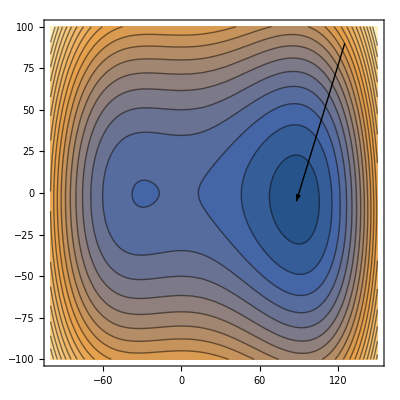

```mathematica
Show[
ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20],
Graphics[{Arrow[{{125,90},{88,-5}}]}]
]//Magnify
```

Compute the Numerical Gradient and Move in That Direction
By numerical gradient, we’re talking about trying one weight --> getting its loss, and trying a nearby weight value --> getting its loss. We adjust our weights by moving proportionally to the difference vector FOR EACH WEIGHT. This method works, it’s just very computationally expensive.

Compute the Symbol Gradient (via Chain Rule) and Move in That Direction

The main way this is done is using the backpropagation of errors algorithm, which is really just a fancy way to say (reverse-mode) chain rule. To do this, most deep learning frameworks (which are more complex, and so need to do things this way) use a model of computational graphs. How does this work? For example,

```mathematica
ComputationalGraphEx[h_]:=Module[{symbols,Transform,panelLabels},
symbols={"X","W1","×","Y","W2","×","+","b","+","-x","e^x","1","+","1/x","J"};
Transform[lbl_]:=Magnify@Rotate[lbl,-π/2];
panelLabels=Table[i->Placed[symbols[[i]],Center,Transform],{i,1,Length[symbols]}];
Graph[{1->3,2->3,4->6,5->6,3->7,6->7,7->9,8->9,9->10,10->11,11->13,12->13,13->14,14->15},VertexSize->Large,VertexLabels->panelLabels,GraphLayout->"LayeredDigraphEmbedding",ImageSize->Large]//Rotate[#,π/2]&
];
ComputationalGraphEx[]:=ComputationalGraphEx[{}];
```

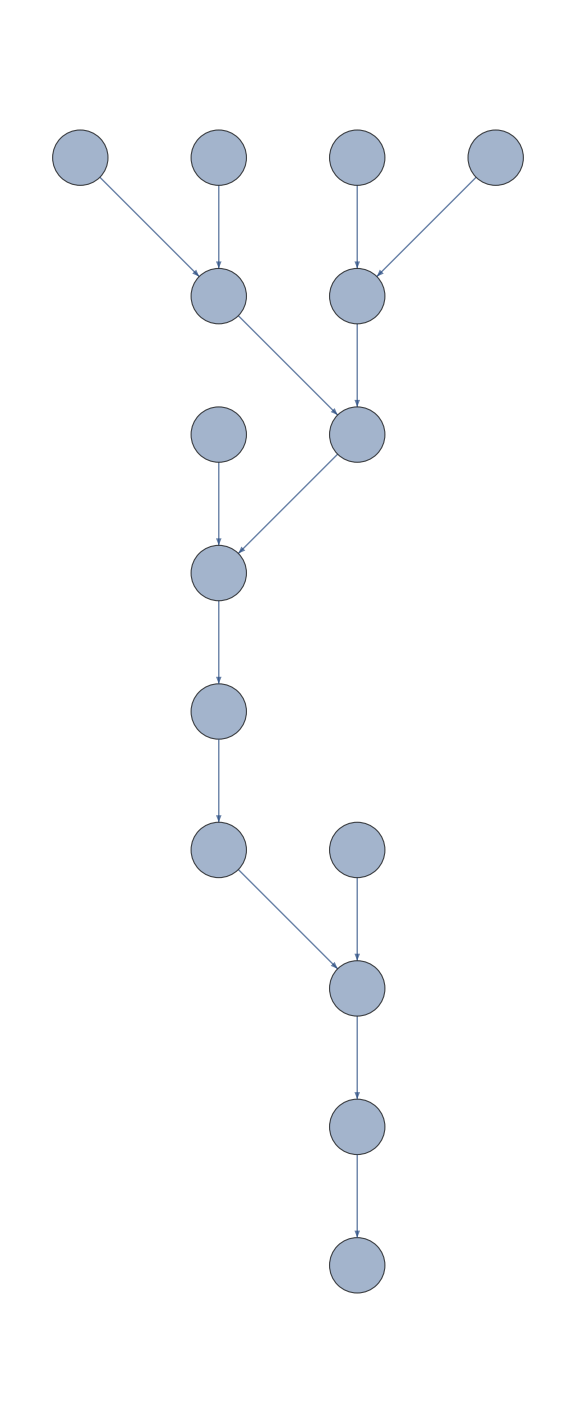

```mathematica
ComputationalGraphEx[]//Magnify
```

Can you guess what function this is for?

So in calculus, the derivative calculates the direction of greatest increase, in each direction. The gradient is such a vector of the (partial) derivatives for each component direction. Symbolically, our J(x,y) has a gradient of

```mathematica
(Jgrad=D[J[x,y],{{x,y}}])//MatrixForm//Magnify
```

(0.001 (10-102 x-2.4 x^2+0.04 x^3)+0.0002 x y
0.0001 x^2+0.2 y)

But visually,

```mathematica
DynamicModule[{
p={100,90},LossLandscape,LossContour},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}+Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]
],
Show[
LossContour,
Graphics[Locator[Dynamic[p]]],
Graphics[Arrow[Dynamic[{p,p+Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
]
]
```

But we don’t want a hill-climbing algorithm, we’re trying to minimize. So we just move in the opposite direction.

```mathematica
DynamicModule[{
p={100,90},LossLandscape,LossContour},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]
],
Show[
LossContour,
Graphics[Locator[Dynamic[p]]],
Graphics[Arrow[Dynamic[{p,p-Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
]
]
```

So to get better and better results, we just take a step in the direction of the gradient until we stop moving.

```mathematica
DynamicModule[{
p={110,100},LossLandscape,LossContour,step=0},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
(*Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]*)
],
Show[
LossContour,
Graphics[Arrow[Dynamic[{p,p-Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
],
Button["STEP",p=p-Jgrad/.{x->p[[1]],y->p[[2]]}]//Magnify,
Button["RESET",p={110,100}]//Magnify
]
]
```

Yay! We’ve reached a global minimum. This is a nice example, though. How could this go wrong? Well, let’s start from a different initial point.

```mathematica
DynamicModule[{
p={-100,0},LossLandscape,LossContour,step=0},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
(*Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]*)
],
Show[
LossContour,
Graphics[Arrow[Dynamic[{p,p-Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
],
Button["STEP",p=p-Jgrad/.{x->p[[1]],y->p[[2]]}]//Magnify,
Button["RESET",p={-100,0}]//Magnify
]
]
```

Hmm...that’s not the minimum we wanted. It’s decent, but we know we can do better. How do we not get stuck in local minima? One way is to just make bigger steps (not usually used in practice; I’ll explain why next). We want to try and overshoot any local minimum along the way.

```mathematica
DynamicModule[{
p={-100,0},LossLandscape,LossContour,step=0},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
(*Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]*)
],
Show[
LossContour,
Graphics[Arrow[Dynamic[{p,p-2Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
],
Button["STEP",p=p-2Jgrad/.{x->p[[1]],y->p[[2]]}]//Magnify,
Button["RESET",p={-100,0}]//Magnify
]
]
```

We just made it over that hill. That worked, so why isn’t this used in practice? Well, there might be a problem with step sizes that are too big; they might make the algorithm diverge.

```mathematica
DynamicModule[{
p={50,-50},LossLandscape,LossContour,step=0},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
(*Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]*)
],
Show[
LossContour,
Graphics[Arrow[Dynamic[{p,p-7Jgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
],
Button["STEP",p=p-7Jgrad/.{x->p[[1]],y->p[[2]]}]//Magnify,
Button["RESET",p={50,-50}]//Magnify
]
]
```

If we needed a high learning rate (as this factor is called) to get over a local minimum, then it might make us keep overshooting and never converging fully.

The typical strategy to solve this is momentum. Not only do we make a step in the direction of the gradient, but we also keep moving in the same direction as we’ve been moving so far (similar to a momentum in physics). The vanilla update algorithm we’ve been using is actually this:

	(x
y)=(x
y) - α  ∇J(x,y)
	
	where α is the learning rate.

When we add momentum, we update our weights by a weighted sum of our momentum so far and our gradient. It look like this:

	(v_x
v_y)=μ (v_x
v_y) - α  ∇J(x,y)		// this is like integrating to get our velocity; we lose velocity over time using a decay rate μ
	(x
y)=(x
y)+(v_x
v_y)				// this is like integrating to get to position

```mathematica
DynamicModule[{
p={-100,0},v={0,0},LossLandscape,LossContour,step=0},
LossLandscape=Plot3D[J[x,y],{x,-100,150},{y,-100,100},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[J[x,y],{x,-100,150},{y,-100,100},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
],
Show[
LossContour,
Graphics[{
Arrow[Dynamic[{p,p-Jgrad/.{x->p[[1]],y->p[[2]]}}]],
Red,
Arrow[Dynamic[{p,p+2v}]]
}]
]
}},ImageSize->Full]
],
Button["STEP",v=0.5v-Jgrad/.{x->p[[1]],y->p[[2]]};p=p+v]//Magnify,
Button["RESET",p={-100,0}]//Magnify
]
]
```

That looks so much better! We’ve reached and converged on the global optima, even though we didn’t have to have a high learning rate to jump fully over the hill. At one point, the gradient actually points in the opposite direction that we want to go, but our momentum keeps up moving forward!

Okay, we’ve generally solved that issue (if we can find good hyperparameters); let’s take a look at another, using a different loss landscape.

In comes the Pringle’s Chip-ish! Our goal is to fall into either of the two wells.

```mathematica
DynamicModule[{
p={0,1},PC,PCgrad,LossLandscape,LossContour,step=0},
PC[x_,y_]:=x^4+y^2-x^2;
PCgrad=D[PC[x,y],{{x,y}}];
LossLandscape=Plot3D[PC[x,y],{x,-1,1},{y,-1,1},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[PC[x,y],{x,-1,1},{y,-1,1},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],20},{p[[1]],p[[2]],0}}]}]
(*Graphics3D[Arrow[Dynamic[{{p[[1]],p[[2]],J[p[[1]],p[[2]]]},{p[[1]],p[[2]],J[p[[1]],p[[1]]]}-Flatten[{Jgrad/.{x->p[[1]],y->p[[2]]},0}]}]]]*)
],
Show[
LossContour,
Graphics[Arrow[Dynamic[{p,p-0.1PCgrad/.{x->p[[1]],y->p[[2]]}}]]]
]
}},ImageSize->Full]
],
Button["STEP",p=p-0.1PCgrad/.{x->p[[1]],y->p[[2]]}]//Magnify,
Button["RESET",p={0,1}]//Magnify
]
]
```

Hmm...okay... This is really frustrating. We can’t seem to get the point to move any lower, because the gradient along that middle hyperplane is always 0. And we only have  2 controls, RESET and STOP, so it’s not like we can do anything more. But maybe there are more advanced gradient update algorithms that can fix this. Let’s try that momentum thing again here.

```mathematica
DynamicModule[{
p={0,1},v={0,0},PC,PCgrad,LossLandscape,LossContour,step=0},
PC[x_,y_]:=x^4+y^2-x^2;
PCgrad=D[PC[x,y],{{x,y}}];
LossLandscape=Plot3D[PC[x,y],{x,-1,1},{y,-1,1},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[PC[x,y],{x,-1,1},{y,-1,1},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
],
Show[
LossContour,
Graphics[{
Arrow[Dynamic[{p,p-0.1PCgrad/.{x->p[[1]],y->p[[2]]}}]],
Red,
Arrow[Dynamic[{p,p+2v}]]
}]
]
}},ImageSize->Full]
],
Button["STEP",v=0.5v-0.1PCgrad/.{x->p[[1]],y->p[[2]]};p=p+v]//Magnify,
Button["RESET",p={0,1}]//Magnify
]
]
```

Nope, that doesn’t help. It turns out, this is still an active area of research. We’ll discuss two options here

Second Order Approximation
The idea with this one is that the second order approximations of the Taylor series probably aren’t 0, so we can use them to move past saddle points. We won’t be visualizing this one.

Noisy Gradient Descent
We add a little bit of noise to get us off the well-trod path.

This is pretty simple to do actually. We just add a bit of random noise to our velocity, almost like we’re just “wandering around.” We do want to make sure to only add a very small amount of noise, as to not overwhelm the gradient update.

```mathematica
DynamicModule[{
p={0,1},v={0,0},PC,PCgrad,LossLandscape,LossContour,step=0},
PC[x_,y_]:=x^4+y^2-x^2;
PCgrad=D[PC[x,y],{{x,y}}];
LossLandscape=Plot3D[PC[x,y],{x,-1,1},{y,-1,1},ClippingStyle->None,PlotRange->Full];
LossContour=ContourPlot[PC[x,y],{x,-1,1},{y,-1,1},Contours->20];
Manipulate[
Dynamic[
GraphicsGrid[{{
Show[
LossLandscape,
Graphics3D[{Thickness[.025],Line[{{p[[1]],p[[2]],2000},{p[[1]],p[[2]],0}}]}]
],
Show[
LossContour,
Graphics[{
Arrow[Dynamic[{p,p-0.1PCgrad/.{x->p[[1]],y->p[[2]]}}]],
Red,
Arrow[Dynamic[{p,p+2v}]]
}]
]
}},ImageSize->Full]
],
Button["STEP",v=0.5v-0.1PCgrad/.{x->p[[1]]+RandomReal[0.01],y->p[[2]]};p=p+v]//Magnify,
Button["RESET",p={0,1}]//Magnify
]
]
```

And that helped!

## A Real Example: Handwriting Recognition

Ok, enough of this boring function approximation stuff. Real ML engineers and data scientists don’t just look at tabular data. Let’s take a common starting dataset: MNIST handwriting. Let’s do what all good data scientists do when they get a new dataset. Explore! (-atory data analysis).

```mathematica
(* Grab the dataset. *)
mnistResource=ResourceObject["MNIST"];
train=ResourceData[mnistResource,"TrainingData"];
test=ResourceData[mnistResource,"TestData"];
```

Let’s just look at a random sample, to get a feel for what the dataset looks like (we’ll avoid looking at test data until the very end):

```mathematica
RandomSample[train,10]//Magnify[#,2]&
```

{-Graphics-→9,-Graphics-→9,-Graphics-→7,-Graphics-→7,-Graphics-→6,-Graphics-→4,-Graphics-→0,-Graphics-→1,-Graphics-→0,-Graphics-→6}

To a human, it doesn’t look too hard to classify what number each handwriting sample is (though 1’s, 4’s, and 7’s look like they might cause trouble).

A Simple Model: Linear Classification on Vectors

Let’s build a really simple linear classification model on the flattened image. Mathematically, this is the first rendition of our model:
	(w_(1,1) | ... | w_(1,784)
... |   | ...
w_(10,1) | ... | w_(10,784))(x_1
 
...
 
x_784)=(pred_1
...
pred_10)

This means that our model will have 10×784=7,840 weights! While it’s not a lot in most deep learning models, it’s definitely a step up from the 2-parameter model we started with.

```mathematica
testImg=ImageData[train[[1]][[1]]];
```

```mathematica
vec=Flatten[testImg]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.8,0.376471,0.00784314,0.376471,0.803922,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.811765,0.0666667,0.0117647,0.0117647,0.0117647,0.0705882,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.788235,0.109804,0.00784314,0.0117647,0.0627451,0.0862745,0.0117647,0.776471,0.976471,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.960784,0.764706,0.121569,0.0117647,0.00784314,0.0117647,0.207843,0.670588,0.0117647,0.00784314,0.521569,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.360784,0.0117647,0.0117647,0.0117647,0.00784314,0.0117647,0.0117647,0.623529,0.258824,0.00784314,0.345098,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.8,0.0666667,0.00784314,0.00784314,0.254902,0.552941,0.00784314,0.105882,0.815686,0.690196,0.,0.341176,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.811765,0.0666667,0.0117647,0.0117647,0.298039,0.952941,0.705882,0.52549,0.917647,1.,1.,0.00784314,0.0470588,0.803922,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.85098,0.352941,0.00784314,0.0862745,0.184314,0.670588,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.352941,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.972549,0.301961,0.0117647,0.0588235,0.721569,0.92549,0.890196,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.235294,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.776471,0.0117647,0.0117647,0.752941,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.235294,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.223529,0.00784314,0.254902,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.00784314,0.231373,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.701961,0.0352941,0.0117647,0.560784,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.00784314,0.0117647,0.419608,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0980392,0.901961,1.,1.,1.,1.,1.,1.,1.,1.,0.972549,0.470588,0.00784314,0.270588,0.952941,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.12549,1.,1.,1.,1.,1.,1.,1.,1.,0.972549,0.486275,0.0117647,0.117647,0.721569,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.431373,1.,1.,1.,1.,1.,1.,1.,0.811765,0.352941,0.0117647,0.321569,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.662745,0.00784314,0.117647,1.,1.,1.,1.,1.,1.,0.552941,0.0666667,0.00784314,0.364706,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0235294,0.427451,0.811765,0.886275,0.666667,0.301961,0.117647,0.00784314,0.12549,0.345098,0.780392,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.666667,0.0117647,0.0117647,0.0117647,0.101961,0.156863,0.0117647,0.0117647,0.0117647,0.231373,0.490196,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.890196,0.219608,0.0117647,0.0117647,0.00784314,0.0117647,0.0117647,0.0862745,0.431373,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.901961,0.498039,0.0117647,0.00784314,0.0117647,0.447059,0.854902,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Length[vec]
```

784

So our preprocessing pipeline so far is this:

```mathematica
GetBatch[d_,i_]:=Module[{flattened,class},
(* flatten the image into a vector *)
flattened=Flatten[ImageData[d[[i]][[1]]]];

(* retrieve the class from the dataset *)
class=d[[i]][[2]];

flattened->class
];
GetBatch[train,1]
```

SetDelayed::write: Tag Real in 6.62325[d_,i_] is Protected.

4.90137[{-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,59792,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9,-Graphics-→9},1]
 |  |  |  |